```mathematica
ClearAll["`*"]
```

task 1 here

```mathematica
dist1[x_] :=PDF[DiscreteUniformDistribution[{1, 4}],x]
```

```mathematica
dist2[x_] :=PDF[DiscreteUniformDistribution[{1, 6}],x]
```

```mathematica
dist3[x_] :=PDF[DiscreteUniformDistribution[{1, 8}],x]
```

```mathematica
dist4[x_] :=PDF[DiscreteUniformDistribution[{1, 12}],x]
```

```mathematica
dist5[x_] :=PDF[DiscreteUniformDistribution[{1, 20}],x]
```

```mathematica
pf1[s_]= pf1[s]=DiscreteConvolve[dist1[y], dist2[y], y, s]
```

Piecewise[{{1/24, s==2||s==10}, {1/12, s==3||s==9}, {1/8, s==4||s==8}, {1/6, 5≤s≤7}, {0, True}}]

```mathematica
pf2[s_]= pf2[s]=DiscreteConvolve[pf1[y], dist3[y], y, s]
```

Piecewise[{{1/192, s==3||s==18}, {1/64, s==4||s==17}, {1/32, s==5||s==16}, {5/96, s==6||s==15}, {7/96, s==7||s==14}, {3/32, s==8||s==13}, {7/64, s==9||s==12}, {23/192, 9<s<12}, {0, True}}]

```mathematica
pf3[s_]= pf3[s]=DiscreteConvolve[pf2[y], dist4[y], y, s]
```

Piecewise[{{1/2304, s==4||s==30}, {1/576, s==5||s==29}, {5/1152, s==6||s==28}, {5/576, s==7||s==27}, {17/1152, s==8||s==26}, {13/576, s==9||s==25}, {73/2304, s==10||s==24}, {1/24, s==11||s==23}, {119/2304, s==12||s==22}, {35/576, s==13||s==21}, {79/1152, s==14||s==20}, {43/576, s==15||s==19}, {181/2304, s==16||s==18}, {23/288, s==17}, {0, True}}]

```mathematica
pf4[s_]= pf4[s]=DiscreteConvolve[pf3[y], dist5[y], y, s] (*Result of 1.1*)
```

Piecewise[{{1/46080, s==5||s==50}, {1/9216, s==6||s==49}, {1/3072, s==7||s==48}, {7/9216, s==8||s==47}, {23/15360, s==9||s==46}, {121/46080, s==10||s==45}, {97/23040, s==11||s==44}, {29/4608, s==12||s==43}, {409/46080, s==13||s==42}, {61/5120, s==14||s==41}, {707/46080, s==15||s==40}, {293/15360, s==16||s==39}, {53/2304, s==17||s==38}, {311/11520, s==18||s==37}, {95/3072, s==19||s==36}, {1597/46080, s==20||s==35}, {39/1024, s==21||s==34}, {379/9216, s==22||s==33}, {1007/23040, s==23||s==32}, {211/4608, s==24||s==31}, {1091/23040, s==25||s==30}, {223/4608, s==26||s==29}, {1127/23040, 26<s<29}, {0, True}}]

task 1.2 here

```mathematica
probToWin = Sum[pf4[x], {x, 5, 10}] + Sum[pf4[x], {x, 45, 50}] (* Result of 1.2 *)
```

41/3840

task 1.4 here

```mathematica
bDist := BinomialDistribution[20, probToWin]
```

```mathematica
N[1 - PDF[bDist, 0]] (* This is the result of 1.4 *)
```

0.193208

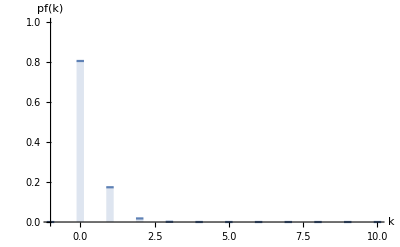

```mathematica
DiscretePlot[PDF[bDist, k], {k, -1, 10}, PlotRange->{Automatic, 1}, AxesLabel->{"k", "pf(k)"}, ExtentSize->0.25]
```

```mathematica
N[(1/probToWin)*2] (* Answer to 1.3 *)
```

187.317

```mathematica
Expectation[pf4[x], x\[Distributed]DiscreteUniformDistribution[{1, 50}]]
```

1/50

```mathematica
KonvTable = Table[pf4[k], {k, 0, 50}];
KonvTable2 = ListConvolve[KonvTable, KonvTable, {1, -1}, 0];
KonvTable3 = ListConvolve[KonvTable2, KonvTable, {1, -1}, 0];
KonvTable4 = ListConvolve[KonvTable3, KonvTable, {1, -1}, 0];
KonvTable5 = ListConvolve[KonvTable4, KonvTable, {1, -1}, 0];
KonvTable6 = ListConvolve[KonvTable5, KonvTable, {1, -1}, 0];
KonvTable7 = ListConvolve[KonvTable6, KonvTable, {1, -1}, 0];
KonvTable8 = ListConvolve[KonvTable7, KonvTable, {1, -1}, 0];
KonvTable9 = ListConvolve[KonvTable8, KonvTable, {1, -1}, 0];
KonvTable10 = ListConvolve[KonvTable9, KonvTable, {1, -1}, 0];
```

```mathematica
Length[KonvTable10]
```

501

```mathematica
probToWinCar = ∑_(x=51)^201 KonvTable10[[x]] + ∑_(x=351)^501 KonvTable10[[x]];
```

```mathematica
N[probToWinCar]
```

0.00118278

```mathematica
N[(1/probToWinCar)*250]
```

211366.

```mathematica
expValTeddy = Sum[k*pf4[k], {k, 5, 50}]
```

55/2

```mathematica
stdDeviationTeddy = Sqrt[Sum[k^2 * pf4[k], {k, 5, 50}] - expValTeddy^2]
```

(√(655/3))/2

```mathematica
expValCar = Sum[k*KonvTable10[[k]], {k , 51, 501}]
```

276